# Комиссаров А . Е лаб2

## 1

```mathematica
1. Придумайте и определите символьное выражение, содержащее не менее трех слагаемых, причем хотя бы одно из них дб рациональным выражением
```

```mathematica
t1=(26*(x^3-3)*(x^3-y^2))/((6*x^3-2)*(x-y))+(x+y)^3+x^2+y^3;
Expand[t1]
```

x^2+x^3-(78 x^3)/((-2+6 x^3) (x-y))+(26 x^6)/((-2+6 x^3) (x-y))+3 x^2 y+3 x y^2+(78 y^2)/((-2+6 x^3) (x-y))-(26 x^3 y^2)/((-2+6 x^3) (x-y))+2 y^3

```mathematica
ExpandAll[t1]
```

x^2+x^3+3 x^2 y+3 x y^2+2 y^3-(78 x^3)/(-2 x+6 x^4+2 y-6 x^3 y)+(26 x^6)/(-2 x+6 x^4+2 y-6 x^3 y)+(78 y^2)/(-2 x+6 x^4+2 y-6 x^3 y)-(26 x^3 y^2)/(-2 x+6 x^4+2 y-6 x^3 y)

```mathematica
Factor[t1]
```

(-40 x^3-x^4+16 x^6+3 x^7+x^2 y-2 x^3 y-3 x^5 y+6 x^6 y+39 y^2-13 x^3 y^2+x y^3-3 x^4 y^3+2 y^4-6 x^3 y^4)/((-1+3 x^3) (x-y))

```mathematica
Together[t1]
```

(-40 x^3-x^4+16 x^6+3 x^7+x^2 y-2 x^3 y-3 x^5 y+6 x^6 y+39 y^2-13 x^3 y^2+x y^3-3 x^4 y^3+2 y^4-6 x^3 y^4)/((-1+3 x^3) (x-y))

```mathematica
Apart[t1]
```

(x (-39-x-x^2+13 x^3+3 x^4+3 x^5))/(-1+3 x^3)+((-39-3 x^2+13 x^3+9 x^5) y)/(-1+3 x^3)+3 x y^2+2 y^3-(13 (3 x^2-3 x^3-x^5+x^6))/((-1+3 x^3) (-x+y))

```mathematica
Cancel[t1]
```

x^2+y^3+(x+y)^3+(13 (-3+x^3) (x^3-y^2))/((-1+3 x^3) (x-y))

```mathematica
Simplify[t1]
```

x^2+y^3+(x+y)^3+(13 (-3+x^3) (x^3-y^2))/((-1+3 x^3) (x-y))

## 2

```mathematica
t2=Numerator[Together[t1]];
t2
```

-40 x^3-x^4+16 x^6+3 x^7+x^2 y-2 x^3 y-3 x^5 y+6 x^6 y+39 y^2-13 x^3 y^2+x y^3-3 x^4 y^3+2 y^4-6 x^3 y^4

```mathematica
Collect[t2,x]
(* Collect представляет в виде полинома по степеням *)
```

3 x^7+x^2 y-3 x^5 y+39 y^2+x y^3+2 y^4+x^6 (16+6 y)+x^4 (-1-3 y^3)+x^3 (-40-2 y-13 y^2-6 y^4)

```mathematica
Collect[t2,y]
```

-40 x^3-x^4+16 x^6+3 x^7+(x^2-2 x^3-3 x^5+6 x^6) y+(39-13 x^3) y^2+(x-3 x^4) y^3+(2-6 x^3) y^4

```mathematica
Exponent[t2,y]
Exponent[t2,x]
```

4

7

```mathematica
Coefficient[t2,x,3]
(*Берёт все X^3 и выводит коэффициенты*)
```

-40-2 y-13 y^2-6 y^4

# 2

## 1

```mathematica
D[x^n*Cos[x], x] (*D от слова derivative - производная*)
```

n x^(-1+n) Cos[x]-x^n Sin[x]

```mathematica
D[(a*x^3+2*x^2),x]
```

4 x+3 a x^2

```mathematica
D[(4*x^2-5*x+8-3/x),{x,3}]
```

18/x^4

```mathematica
D[(x^3*y^2+3*x^2),{x,3},{y,2}]
```

12

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
res = x^3/(x^2+1);
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
resBack = Together[D[x^2/2-1/2 Log[1+x^2],x]]
```

x^3/(1+x^2)

```mathematica
res2 := 1/(x^3+1);
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
resBack2 = Simplify[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]
```

1/(1+x^3)

```mathematica
Integrate[5*x-2*√x+32/x^3, {x,1,4}]
```

259/6

```mathematica
N[Integrate[(1+x^4)^(1/3), {x,0,1}],25]
```

1.057527731779011858114859

```mathematica
Integrate[(1+x^4)^(1/3),{x,0,1.}]
```

1.05753

```mathematica
3
```

```mathematica
Solve[a*x^4+x^2+3==0, x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

```mathematica
Solve[x^2+y==1 && y^2-x^2==2,{x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

```mathematica
Solve[x^2-y^2==1 && y^3+x==5,{x,y}]
```

{{x→5-(Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025)^3,y→Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025},{x→5-(Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715)^3,y→Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715},{x→5-(Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702)^3,y→Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702},{x→5-(Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702)^3,y→Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702},{x→5-(Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017)^3,y→Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017},{x→5-(Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017)^3,y→Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017}}

```mathematica
NSolve[x^2-y^2==1 && y^3+x==5,{x,y},Reals]
```

{{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285}}

```mathematica
result = DSolve[y'[x]-y[x]*Tan[x]==x,y[x],x]
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
result2 = DSolve[y'[x]+y[x]*Tan[x]==1/Cos[x],y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

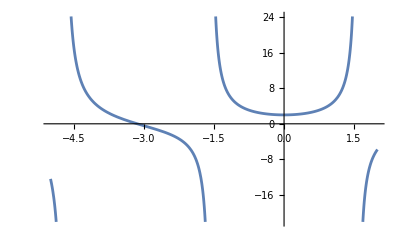

```mathematica
Plot[Evaluate[y[x]/. result /. {C[1] ->1}],{x,-5,2}]
```

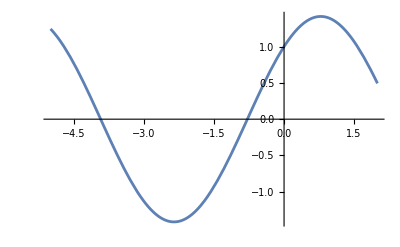

```mathematica
Plot[Evaluate[y[x]/. result2 /. {C[1] ->1}],{x,-5,2}]
```

```mathematica
t3= DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==2, y'[0]==3}, y[x], x]//FullSimplify
```

{{y[x]→2 ⅇ^(x/2) π (-((AiryAi[1/4]+AiryAiPrime[1/4]) AiryBi[1/4-x])+AiryAi[1/4-x] (AiryBi[1/4]+AiryBiPrime[1/4]))}}

```mathematica
t4 = NDSolve[{y''[x]-y'[x]+x* y[x]==0, y[0]==2, y'[0]==3}, y[x], {x, -5,5}]
```

{{y[x]→InterpolatingFunction[…][x]}}

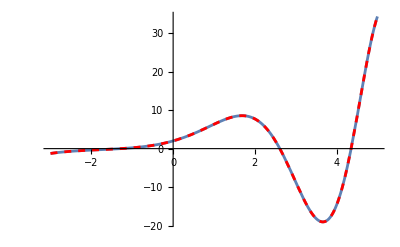

```mathematica
Show[Plot[t3[[1,1,2]],{x,-3,5}], Plot[t4[[1, 1, 2]], {x, -3, 5},PlotStyle->{Dashed, Red}]]
```